# Integration and Monte Carlo Michael Calmette

## The Basic Integration Modules

### Box Integration

Integral takes, as input, a function f, the lower and upper integration limits (x and x) and the number of rectangles used in the approximation N.

```mathematica
F[x_]:=(x^2)/2;
BoxIntegration[F_,x0_,xf_,Ns_]:=Module[{dA,dx,xa,NN,val},
NN=0;
dx = (xf-x0)/Ns;
xa=x0+dx;
val=0;
While[NN<Ns,NN++;
xa=x0+(NN*dx);
val=val+F[xa]*dx;
];
Return[val];
]
BoxIntegration[F,-1,3,100]
Plot[F[x],{x,-1,3},Filling->Bottom]
```

2967/625

-Graphics-

### Trapezoid Integration

```mathematica
TrapIntegration[F_,x0_,xf_,Ns_]:=Module[{dA,dx,xa,NN,val,sum},
NN=0;
dx = (xf-x0)/Ns;
xa=x0+dx;
val=0;
While[NN<Ns,NN++;
xa=x0+(NN*dx);
val=val+.5*(F[xa]+F[xa-dx])*dx;
];
Return[val];
]
TrapIntegration[F,-1,3,100]
Plot[F[x],{x,-1,3},Filling->Bottom]
```

4.6672

-Graphics-

### Testing

Test both modules on the function

f(x) = x

with the limits of integration [-1, 3], and N = 100.  Compare each result to the analytic result.

```mathematica
F[x_]:=(x^2)/2;
BoxIntegration[F,-1,3,100]
TrapIntegration[F,-1,3,100]
Plot[F[x],{x,-1,3},Filling->Bottom]
```

2967/625

4.6672

-Graphics-

```mathematica
(*Answer is 4.6666 repeating, and 2967/625 is equal to 4.7472, so the trapezoid integration is more precise, as expected since it does a better job calculating the area*)
```

## Gaussian Integration

Use our numerical integration method to approximate the Gaussian integral

∫ⅇⅆx

which has known analytic value π.  Here there is an additional challenge because we can’t expect to use ±∞ as inputs for our numerical work.

### Plotting the function

This becomes approximately zero, as it gets further from x = 0.

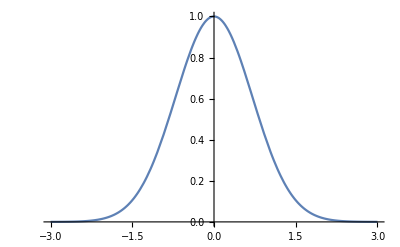

```mathematica
Plot[ⅇ^(-x^2),{x,-3,3}]
```

### Evaluating the integral

Using these limits, evaluate the Gaussian integral with your trapezoidal approximation module, and compare the result with the analytic value.

1.77245

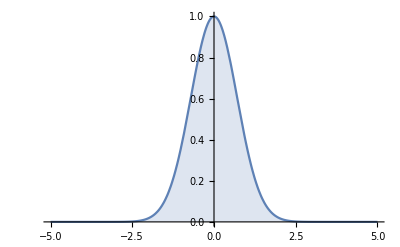

```mathematica
H[x_]:=ⅇ^(-x^2)
TrapIntegration[H_,x0_,xf_,Ns_]:=Module[{dA,dx,xa,NN,val,sum},
NN=0;
dx = (xf-x0)/Ns;
xa=x0+dx;
val=0;
While[NN<Ns,NN++;
xa=x0+(NN*dx);
val=val+.5*(H[xa]+H[xa-dx])*dx;
];
Return[val];
]
TrapIntegration[H,-100,100,100000]
Plot[H[x],{x,-5,5},Filling->Bottom]
```

```mathematica
(*The square root of pi is 1.772453, so they are in agreement with each other.*)
```

### Sources of error

The evaluation you have done actually has two sources of error: the error associated with approximating an integral as a series of trapezoidal areas, and the error associated with cutting off the region of integration.  It’s instructive to know how much each is contributing to the error, and which is most significant.  (This will, of course, depend on your choices of N and the region of integration.)

#### Error from trapezoids

Compute the approximation of the integral for some value of N, and then again for twice that value.  This decreases the width of each trapezoid by 1/2, and should make the approximation better.  Calculate the difference between the two results.

```mathematica
(*Original*)NumberForm[TrapIntegration[H,-100,100,100000],20]
(*Double N*)NumberForm[TrapIntegration[H,-100,100,200000],20]
Y=TrapIntegration[H,-100,100,200000]-TrapIntegration[H,-100,100,100000];
Print["The difference is: ", Y]
```

1.772453850905515

1.772453850905509

The difference is: -5.77316×10^-15

#### Error from truncation

```mathematica
(*Original*)NumberForm[TrapIntegration[H,-100,100,100000],20]
(*Double Region*)NumberForm[TrapIntegration[H,-200,200,100000],20]
X=TrapIntegration[H,-100,100,100000]-TrapIntegration[H,-200,200,100000];
Print["The Difference is: ", X]
```

1.772453850905515

1.772453850905515

The Difference is: 2.22045×10^-16

```mathematica
(*What makes a more significant difference is decreasing the width of the trapezoids.  The difference is about a tenth off.*)
```

## The Sinc function

Approximating the integral:

I = ∫Sin(x)ⅆx

A computer will have trouble evaluating it at x = 0.  Evaluate the integral using N = 100.

1.65828

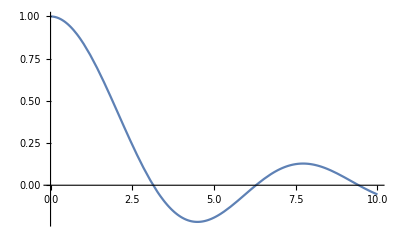

```mathematica
G[x_]:=Sin[x]/x;
SinFunction[G_,x0_,xf_,Ns_]:=Module[{dA,dx,xa,NN,val,sum},
NN=0;
dx = (xf-x0)/Ns;
xa=x0+dx;
val=0;
If[xa-dx==0,G[xa-dx]=1,Print[ error]];
While[NN<Ns,NN++;
xa=x0+(NN*dx);
val=val+.5*(G[xa]+G[xa-dx])*dx;
];
Return[val];
]
SinFunction[G,0,10,100]
Plot[G[x],{x,0,10}]
```

## Simpson’s Method

### The Module

It should take as inputs the function f, limits of integration (x and x), and the number of regions N.  N must be an even integer.

### Testing

Test your module on the same function 
f(x) = x^2/2
that you previously used for the box and trapezoidal integrals.  Note that since this is quadratic, the Simpson method should give the exact correct answer.

```mathematica
F[x_]:=x^2/2;
Simpsons[F_,a_,b_,Ns_]:=Module[{Ia,N,j,dx,Y},
N=Ns/2;
Y=Mod[N,1];
If[Y==0, dx=(b-a)/Ns;
Ia=0.0;
For[j=0,j≤Ns-2,j=j+2, Ia=Ia+(1/3)dx (F[a+j dx]+4F[a+(j+1)dx]+F[a+(j+2) dx])];
Return[Ia];
 , Print["Please use an even number of steps"]];
]
Simpsons[F,-1,3,99]
Simpsons[F,-1,3,100]
```

Please use an even number of steps

4.66667

## Comparing Accuracy

Will use the integral

∫xⅆx

to examine the accuracy.  For each method, the number N, which captures the number of subregions the integration region is split up into, controls how accurate the method is.  Specifically, we have the width of each region Δx ∝ 1, and we expect the amount of error to decrease, the smaller Δx is.

### Box Integration Accuracy

For the box integration method, we expect the amount of error to be proportional to Δx, and thus to be proportional to 1/N.  Compute a table of the results of the box integral for the values N = {100, 110, 120, ..., 1000} (values between 100 and 1000, in steps of 10).  Put it into the form of a list of ordered pairs: {N, I(N)}.  Plot this to confirm that the essential behavior is correct.  Then, use “FindFit” to fit this data to a function in the form a + c/N, and display the plot of the fitted function together with the error data.  (The constant “a” should be the actual value of the integral.)

The necessary steps are given below, but you must update the name of your module for box integration.  I called mine boxint, so just adjust this with whatever yours is called.

```mathematica
ff[x_] := x^5
boxint[ff_,x0_,xf_,Ns_]:=Module[{dA,dx,xa,NN,val},
NN=0;
dx = (xf-x0)/Ns;
xa=x0+dx;
val=0;
While[NN<Ns,NN++;
xa=x0+(NN*dx);
val=val+ff[xa]*dx;
];
Return[val];
]
```

```mathematica
boxerrors = Table[boxint[ff, 0, 1, NN], {NN, 100, 1000, 10}];
```

```mathematica
boxpairs = Table[{10n + 90, boxerrors[[n]]}, {n, 1, Length[boxerrors]}];
```

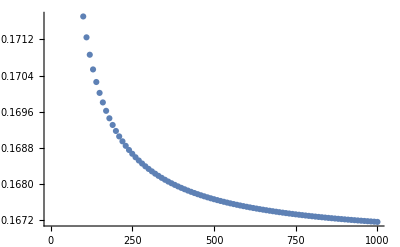

```mathematica
boxplot1 = ListPlot[boxpairs]
```

```mathematica
fit = FindFit[boxpairs, a + c/x, {a, c}, x]
```

{a→0.166662,c→0.503676}

```mathematica
boxerr[x_] := a + c/x /. fit
```

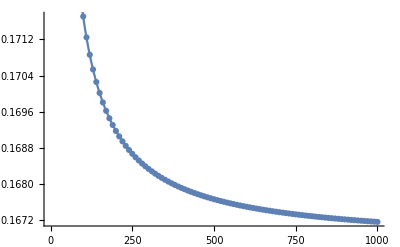

```mathematica
Show[boxplot1, Plot[boxerr[x], {x, 0, 1000}]]
```

### Trapezoid Integration Accuracy

```mathematica
FF[x_] := x^5
TrapInt[FF_,x0_,xf_,Ns_]:=Module[{dA,dx,xa,NN,val,sum},
NN=0;
dx = (xf-x0)/Ns;
xa=x0+dx;
val=0;
While[NN<Ns,NN++;
xa=x0+(NN*dx);
val=val+.5*(FF[xa]+FF[xa-dx])*dx;
];
Return[val];
]
```

```mathematica
boxerrors1 = Table[TrapInt[ff, 0, 1, NN], {NN, 100, 1000, 10}];
```

```mathematica
boxpairs1 = Table[{10n + 90, boxerrors1[[n]]}, {n, 1, Length[boxerrors1]}];
```

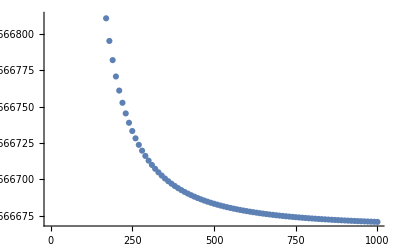

```mathematica
boxplot1a = ListPlot[boxpairs1]
```

```mathematica
fit1 = FindFit[boxpairs1, a + c/x^2, {a, c}, x]
```

{a→0.166667,c→0.41666}

```mathematica
boxerr1[x_] := a + c/x^2 /. fit1
```

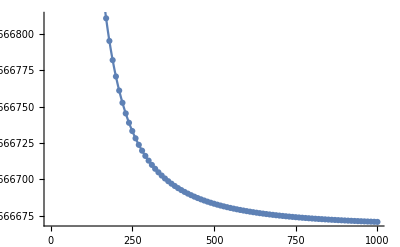

```mathematica
Show[boxplot1a, Plot[boxerr1[x], {x, 0, 1000}]]
```

### Simpson Integration Accuracy

Repeat the process with the Simpson’s method results.

```mathematica
FA[x_]:=x^5;
SimpsonsInt[FA_,a_,b_,Ns_]:=Module[{Ia,N,j,dx,Y},
N=Ns/2;
Y=Mod[N,1];
If[Y==0, dx=(b-a)/Ns;
Ia=0.0;
For[j=0,j≤Ns-2,j=j+2, Ia=Ia+(1/3)dx (FA[a+j dx]+4FA[a+(j+1)dx]+FA[a+(j+2) dx])];
Return[Ia];
 , Print["Please use an even number of steps"]];
]
```

```mathematica
boxerrors2 = Table[SimpsonsInt[FA, 0, 1, NN], {NN, 100, 1000, 10}];
```

```mathematica
boxpairs2 = Table[{10n + 90, boxerrors2[[n]]}, {n, 1, Length[boxerrors2]}];
```

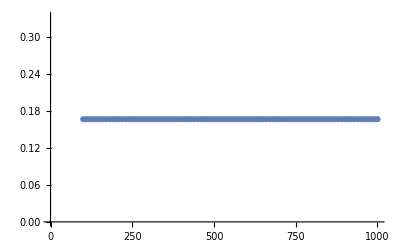

```mathematica
boxplot2a = ListPlot[boxpairs2]
```

```mathematica
fit2 = FindFit[boxpairs2, a + c/x^4, {a, c}, x]
```

{a→0.166667,c→0.333333}

```mathematica
boxerr2[x_] := a + c/x^4 /. fit2
```

```mathematica
Show[boxplot2a, Plot[boxerr2[x], {x, 0, 1000}]]
```

-Graphics-

## Comparing Timing (Skip)

Using the same integral as in the previous section and the same range of values of N, create tables that give the times required to perform each integral.  Plot the times as functions of N for each of the three methods, together on the same graph.  Remember to discuss the results and whether or not they make sense.  As before, update the names of your modules as necessary.

```mathematica
times = Table[{NN, Timing[boxint[ff, 0, 1, NN]][[1]]}, {NN, 100, 1000, 10}];
```

```mathematica
times2 = Table[{NN, Timing[trapint[ff, 0, 1, NN]][[1]]}, {NN, 100, 1000, 10}];
```

```mathematica
times3 = Table[{NN, Timing[simpsonint[ff, 0, 1, NN]][[1]]}, {NN, 100, 1000, 10}];
```

```mathematica
ListPlot[{times, times2, times3}]
```

## The Line of Charge

Here we want to compute and display the electric potential in the vicinity of a line of charge with varying charge density

λ(x) = λⅇ

(a) Create a function V(x, y) that computes the electric potential in dimensionless form as a function of the position in the xy plane for some given values of x and y.  Note that the limits of integration are infinite so you will have to make an intelligent choice about where to cut them off.  To make this choice, first plot dV(x,y,X), where X is your variable of integration.  Vary x and y to see what bounds on X give convergence.  Then, find V(x, y) using Simpson’s method.
(b) Generate a table of values of {x, y, V(x, y)} over the range x ∈ [-5, 5], y ∈ [-5, 5], in steps of size 0.1.  This will take some time to finish evaluating.
(c) Use “ListContourPlot” to display the electric potential graphically.  Note that the contours represent equipotential lines, and therefore that the electric field will be perpendicular to these lines.

(a)

1.32443×10^-8

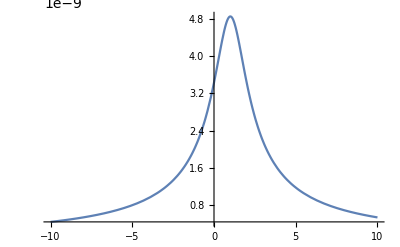

```mathematica
l=8*10^-9;
s=1;
dV[x_,y_,X_] := ((8*10^-9)*(E^((-x^2)/(2*1))))/Sqrt[((x-X)^2 +y^2)]
V[dV_,a_,b_,Ns_,x_,y_]:=Module[{X,Ia,dx},
X=a;
dx=(b-a)/Ns;
Ia=0.0;
For[X=0,X≤Ns-2,X=X+2,
Ia=Ia+(1/3)dx (dV[x,y,X]+4dV[x,y,X+dx]+dV[x,y,X+2* dx]);
X=X+dx;
];
Return[Ia];
]

V[dV,-5,5,3,1,1]
Plot[dV[1,1,X],{X,-10,10}]
```

(b) Don’t want y=0, so split them up and then recombine them

```mathematica
F=Table[{x,y,V[dV,-10,10,2,x,y]},{x,-5,5,.1},{y,-5,-.1,.01}];
S=Table[{x,y,V[dV,-10,10,2,x,y]},{x,-5,5,.1},{y,.1,5,.01}];
joinn=Join[F,S];
pts=Flatten[joinn,1];
```

(c)

```mathematica
ListContourPlot[pts]
```

-Graphics-

## Problem 6.18

```mathematica
MonteCarlo2Area[R_,Ns_]:=Module[{hit,index,x,y},
hit=0;
For[index=1,index≤ Ns, index = index+1,
x=RandomReal[{-R,R}];
y=RandomReal[{-R,R}];
If[Sqrt[x^2+y^2]≤ R,
hit = hit+1;
];
];
Return[(hit/Ns) (2R)^2];
]
MonteCarlo2Area[2.0,1000]
```

12.8

```mathematica
MonteCarlo3Area[R_,Ns_]:=Module[{hit,index,x,y,z},
hit=0;
For[index=1,index≤ Ns, index = index+1,
x=RandomReal[{-R,R}];
y=RandomReal[{-R,R}];
z=RandomReal[{-R,R}];
If[Sqrt[x^2+y^2+z^2]≤ R,
hit = hit+1;
];
];
Return[(hit/Ns) (2R)^3];
]
MonteCarlo3Area[2.0,10000]
```

33.5424

```mathematica
MonteCarlo4Area[R_,Ns_]:=Module[{hit,index,x,y,z,zz},
hit=0;
For[index=1,index≤ Ns, index=index+1,
x=RandomReal[{-R,R}];
y=RandomReal[{-R,R}];
z=RandomReal[{-R,R}];
zz=RandomReal[{-R,R}];
If[Sqrt[x^2+y^2+z^2]≤ R,
hit = hit+1;
];
];
Return[(hit/Ns) (2R)^4];
]
MonteCarlo4Area[2.0,100000]
```

133.256

## N-Diamond

In Problem 6.18, you found the “area” of a sphere in a few different dimensions.  For this problem, we will generalize for any N-dimensional diamond.  By diamond, I mean that the corners of the diamond are found at the midpoints of a larger square (ask me for a picture of this if it’s unclear to you).  Using the Monte Carlo technique, find the area of the diamond for a few different dimensions N.  How many darts do you have to shoot inside of the larger square to ensure 1% precision in your area calculation for the diamond?

```mathematica
MonteCarloNArea[R_,Ns_,Dim_]:=Module[{hit,index,x,y,z,D},
hit=0;
D=Dim;
For[index=1,index≤ Ns, index=index+1,
x=RandomReal[{-R,R}];
y=RandomReal[{-R,R}];
z=RandomReal[{-R,R}];

If[Sqrt[(x^2+y^2+z^2)]≤R,
hit=hit+1;
];
];
Return[(hit/Ns) (2R)^D];
]
MonteCarloNArea[2.0,50,4]
```

158.72